## How to run the Yukawa package

## Run packages (Just run everything)

```mathematica
(* Change the following line to the Δmax you set. 
Δmax=6 can be done instantly but cannot be used to reproduce the figures. 
The figures require Δmax ≥ 20.
For example, Δmax=21 takes about 5 hours on a laptop. *)
ClearAll["Global`*"];
Δmax=6;
```

```mathematica
$HistoryLength=5;
$MaxExtraPrecision = 100;
SetDirectory[NotebookDirectory[]];
Get[NotebookDirectory[]<>"GenerateBasis-N1Susy.wl"];
Get[NotebookDirectory[]<>"MatrixElements-Mixon-Mass.wl"];
Get[NotebookDirectory[]<>"MatrixElements-Mixon-Phi4.wl"];
Get[NotebookDirectory[]<>"MatrixElements-Mixon-Phi3.wl"];
Get[NotebookDirectory[]<>"MatrixElements-Yukawa.wl"];
Get[NotebookDirectory[]<>"MatrixElements-QMinus.wl"];
Get[NotebookDirectory[]<>"MatrixElements-QPlus.wl"];
```

```mathematica
computeN1SUSYBasis[Δmax,NotebookDirectory[],MachinePrecision];
computeMixonMassMatrices[Δmax,basisN1SUSY,NotebookDirectory[]]; 
computePhi4Matrices[Δmax,basisN1SUSY,NotebookDirectory[]];
computePhi3Matrices[Δmax,basisN1SUSY,NotebookDirectory[]];
computeYukawaMatrices[Δmax,basisN1SUSY,NotebookDirectory[]];
computeQMinusMatrix[Δmax,basisN1SUSY,NotebookDirectory[]];
computeQPlusMatrix[Δmax,basisN1SUSY,NotebookDirectory[]];
```

@ : Generating boson states

t=0.00003

n@ 1

t=0.00016

n@ 2

t=0.053813

n@ 3

t=0.055561

n@ 4

t=0.057237

n@ 5

t=0.058131

n@ 6

t=0.058697

@ : Generating fermion states

@ :1

Time (m):5.01667×10^-6

@ :2

Time (m):0.000109683

@ :3

Time (m):0.000118

@ :4

Time (m):0.000164

@ :5

Time (m):0.00017715

@ :6

Time (m):0.000184067

@ : taking boson descendants

Time (s):0.079802

@ : taking fermion descendants

Time (s):0.081201

@ : gluing fermion and bosons

Time (s):0.083761

@ scalar mass:

t = 0.040908

@ fermion mass:

t = 0.077964

@ NtoN:

t = 0.056953

@ N to N+2:

t = 0.088568

@ N to N+1:

t = 0.046406

@ Quartic:

t = 0.28802

@ Cubic:

t = 0.364362

t = 0.040135

Q+ mass term ,t = 0.04191

Q+ interaction term, t = 0.11243

DeleteFile::fdnfnd: Directory or file MatrixQPlusMassD6 not found.

DeleteFile::fdnfnd: Directory or file MatrixQPlusIntD6 not found.

```mathematica
(* If you get the error message saying QP matrix is not found and cannot be deleted, it is fine. *)
```

## Parse the computed data into readable forms

Make a 1-D list of all states

```mathematica
flattenedStates=Block[
{kets,projection},
kets=Flatten[If[Length[#states]>1,Table[ReplacePart[#,-1->{#states[[idx]]}],{idx,Length[#states]}],#]&/@Flatten[basisN1SUSY]]
];
```

Let’s see the info of the beginning 5 states

```mathematica
flattenedStates[[;;5]]
```

{<|nB→0,degB→0,nF→1,degF→0,l→0,states→{{{{1.}}}}|>,<|nB→0,degB→0,nF→2,degF→1,l→0,states→{{{{1.}}}}|>,<|nB→0,degB→0,nF→2,degF→3,l→0,states→{{{{0.408248,-0.912871}}}}|>,<|nB→0,degB→0,nF→3,degF→3,l→0,states→{{{{1.}}}}|>,<|nB→1,degB→0,nF→0,degF→0,l→0,states→{{{{1.}}}}|>}

The purpose of the following is to undo the nested structure of the stored matrix element and give a single big matrix where the states are ordered in the same way as the list flattendStates.

```mathematica
takeNonEmpty[mat_]:=Block[
	{flattened=Flatten[mat,{{1,3},{2,4}}],idxNull, i=0},
	idxNull=Position[Diagonal[flattened],{}];
	(*Delete[Transpose[Delete[flattened,idxNull]],idxNull]*)
	Fold[Drop[#1,#2-i,#2-(i++)]&,flattened,idxNull]
];
sparseArrayFlatten[mat_]:=Block[
{dims=Map[Dimensions,mat,{2}],
rows,cols,res},
rows=Prepend[dims[[;;,1,1]]//Accumulate,0];
cols=Prepend[dims[[1,;;,2]]//Accumulate,0];
res=Sum[SparseArray[
Band[{ (rows[[i]]+1),(cols[[j]]+1)},{rows[[i+1]],cols[[j+1]]}]->mat[[i,j]],
{Last[rows],Last[cols]}],
{i,Length[rows]-1},{j,Length[cols]-1}
];
res
];
(* Scalar mass term *)
Hms=takeNonEmpty[matScalarMass]//sparseArrayFlatten;
(* Fermion mass term *)
Hmf=takeNonEmpty[matFermionMass]//sparseArrayFlatten;
(* ϕ^3 term *)
HNN1=takeNonEmpty[matPhi3NtoN1]//sparseArrayFlatten;
(* ϕ^4 N to N term *)
HNN=takeNonEmpty[matPhi4NtoN]//sparseArrayFlatten;
(* ϕ^4 N to N±2 term *)
HNN2=takeNonEmpty[matPhi4NtoN2]//sparseArrayFlatten;
(* Yukawa cubic term *)
HY3=takeNonEmpty[matYukawaCubic]//sparseArrayFlatten;
(* Yukawa quartic term *)
HY4=takeNonEmpty[matYukawaQuartic]//sparseArrayFlatten;
(* Supercharge Q_- : (∂ϕ)ψ *)
QM=takeNonEmpty[matQMinus]//sparseArrayFlatten;
(* Supercharge Q_+ mass term: ϕψ *)
QP2=takeNonEmpty[matQPlusMass]//sparseArrayFlatten;
(* Supercharge Q_+ interaction term: ϕ^2 ψ *)
gRatio=1/(4 √π); 
QP3=gRatio*takeNonEmpty[matQPlusInt]//sparseArrayFlatten;
(* In SUSY we want Q_+^2 == P_+ . If we multiply this factor to the matrix elements we computed in Q_+ interaction term, then the coupling g has the same meaning in all the matrices above. *)
```

## Save data in more compact format

```mathematica
(* This saves and loads the data as .WXF files. *)
binarySave[name_,expr_]:=Export[name<>".WXF",BinarySerialize[expr]];
binaryGet[name_]:=Import[name]//BinaryDeserialize;
```

```mathematica
binarySave["QM_"<>ToString[Δmax],QM]
binarySave["QP2_"<>ToString[Δmax],QP2]
binarySave["QP3_"<>ToString[Δmax],QP3]
```

QM_6.WXF

QP2_6.WXF

QP3_6.WXF

```mathematica
binarySave["Hms_"<>ToString[Δmax],Hms]
binarySave["Hmf_"<>ToString[Δmax],Hmf]
binarySave["HNN1_"<>ToString[Δmax],HNN1]
binarySave["HNN_"<>ToString[Δmax],HNN]
binarySave["HNN2_"<>ToString[Δmax],HNN2]
binarySave["HY3_"<>ToString[Δmax],HY3]
binarySave["HY4_"<>ToString[Δmax],HY4]
```

Hms_6.WXF

Hmf_6.WXF

HNN1_6.WXF

HNN_6.WXF

HNN2_6.WXF

HY3_6.WXF

HY4_6.WXF

## Load previously computed data and parse

```mathematica
ClearAll["Global`*"]
```

```mathematica
binarySave[name_,expr_]:=Export[name<>".WXF",BinarySerialize[expr]];
binaryGet[name_]:=Import[name]//BinaryDeserialize;
```

```mathematica
(* Load the Δmax=21 data. The data can be used for any smaller Δmax. *)
SetDirectory[NotebookDirectory[]]
flattenedStates=binaryGet["states_21.WXF"];
HmsBeforeCut=binaryGet["Hms_21.WXF"];
HmfBeforeCut=binaryGet["Hmf_21.WXF"];
HNNBeforeCut=binaryGet["HNN_21.WXF"];
HNN1BeforeCut=binaryGet["HNN1_21.WXF"];
HNN2BeforeCut=binaryGet["HNN2_21.WXF"];
HY3BeforeCut=binaryGet["HY3_21.WXF"];
HY4BeforeCut=binaryGet["HY4_21.WXF"];
QP3BeforeCut=binaryGet["QP3_21.WXF"];
```

/Users/yuan/Dropbox/Lightcone Collaborations/Sandbox/PublicCode/to_add/yukawa

```mathematica
(* Cut the matrices into lower Δmax *)
cut[Δmax_]:=Flatten@Position[flattenedStates,assoc_/;(dimOf[assoc])≤Δmax,1,Heads->False];
dimOf=(#degB+#degF+#nB+#nF+#l)&;
(* Scalar mass term *)
Hms[Δmax_]:=Hms[Δmax]=HmsBeforeCut[[cut[Δmax],cut[Δmax]]];
(* Fermion mass term *)
Hmf[Δmax_]:=Hmf[Δmax]=HmfBeforeCut[[cut[Δmax],cut[Δmax]]];
(* Yukawa cubic term *)
HY3[Δmax_]:=HY3[Δmax]=HY3BeforeCut[[cut[Δmax],cut[Δmax]]];
(* Yukawa quartic term *)
HY4[Δmax_]:=HY4[Δmax]=HY4BeforeCut[[cut[Δmax],cut[Δmax]]];
(* ϕ^4 N to N term *)
HNN[Δmax_]:=HNN[Δmax]=HNNBeforeCut[[cut[Δmax],cut[Δmax]]];
(* ϕ^3 term *)
HNN1[Δmax_]:=HNN1[Δmax]=HNN1BeforeCut[[cut[Δmax],cut[Δmax]]];
(* ϕ^4 N to N±2 term *)
HNN2[Δmax_]:=HNN2[Δmax]=HNN2BeforeCut[[cut[Δmax],cut[Δmax]]];
(* Supercharge Q_+ interaction term: ϕ^2 ψ *)
QP3[Δmax_]:=QP3[Δmax]=QP3BeforeCut[[cut[Δmax],cut[Δmax]]];
(* QM and QP2 not used in Non-SUSY Yukawa project *)
(*QP2BeforeCut=binaryGet["QP2_21.WXF"];
QP2[Δmax_]:=QP2[Δmax]=QP2BeforeCut[[cut[Δmax],cut[Δmax]]];*)
(*QM[Δmax_]:=QM[Δmax]=QMBeforeCut[[cut[Δmax],cut[Δmax]]];*)
```

```mathematica
(* Fermion mass counter term *)
ClearAll[counter]
counter[Δmax_]:=counter[Δmax]=Block[{states,qmat},
states=Table[
Position[
flattenedStates[[ cut[Δmax]]],
assoc_/;(#nB==n&@assoc),1,Heads->False]//Flatten,
{n,0,Δmax}];
qmat=QP3[Δmax]*0;
Do[
qmat[[ states[[n+1]], states[[n+3]] ]]=
QP3[Δmax][[ states[[n+1]], states[[n+3]] ]],
{n,0,Δmax-2}
];
qmat.Transpose[qmat]
]
```

```mathematica
(* Scalar mass counter term *)
ClearAll[counterScalar]
counterScalar[Δmax_]:=counterScalar[Δmax]=Block[{states,qmat},
states=Table[
Position[
flattenedStates[[ cut[Δmax]]],
assoc_/;(#nF==n&@assoc),1,Heads->False]//Flatten,
{n,0,Δmax}];
qmat=QP3[Δmax]*0;
Do[
qmat[[ states[[n+1]], states[[n+2]] ]]=
QP3[Δmax][[ states[[n+1]], states[[n+2]] ]],
{n,0,Δmax-1}
];
qmat.Transpose[qmat]
]
```

```mathematica
(* The whole Non-SUSY Yukawa Hamiltonian with both local and local counterterms *)
hamitonian[Δmax_,mf_,ms_,g_]:=With[{Y=1/4,X=1/8*1/4},
ms^2 Hms[Δmax]+mf^2 Hmf[Δmax]+((2g) mf HY3[Δmax]+Y (4 g^2)HY4[Δmax])
+(4g^2)(counter[Δmax]+counterScalar[Δmax])
-g^2/(2π)(Log[ms/mf])Hmf[Δmax]
]
```

## Fermion Mass shift

In this section, we compute the Fermion mass shift at 𝒪(g^2) order in old-fashioned perturbation theory, and reproduce Fig. 20 and Fig. 21 of the paper. Since this is not the final data and the old-fashioned perturbation theory computation is technical, this section can be skipped in first reading.

## Old fashioned perturbation theory

Split the basis by the number of particles

```mathematica
ClearAll[particleSector]
particleSector[nB_,nF_,Δmax_]:=particleSector[nB,nF,Δmax]=Position[
Select[flattenedStates,#degB+#degF+#nB+#nF+#l<=Δmax&],
assoc_/;(#nB==nB&&#nF==nF&[assoc]),1,Heads->False]//Flatten;
```

Compute the zeroth order mass eigenvalues and eigenstates of purely fermions, up to 3 fermions

```mathematica
zeroOrderFermion//ClearAll;
zeroOrderFermion[Δmax_,mf_,ms_]:=zeroOrderFermion[Δmax,mf,ms]=Block[{pos,evals,evecs,nB=0},
Table[
pos=particleSector[nB,nF,Δmax];
{evals,evecs}=Eigensystem[
mf^2 Hmf[Δmax][[pos,pos]]+ms^2 Hms[Δmax][[pos,pos]]
];
<|"nB"->nB,"nF"->nF,"evals"->evals,"evecs"->evecs|>,
{nF,1,3}
] ];
```

Compute the zeroth order mass eigenvalues and eigenstates of 1 boson and up to 3 fermions

```mathematica
zeroOrderOneBoson//ClearAll;
zeroOrderOneBoson[Δmax_,mf_,ms_]:=zeroOrderOneBoson[Δmax,mf,ms]=Block[{pos,evals,evecs,nB=1},
Table[
pos=particleSector[nB,nF,Δmax];
{evals,evecs}=Eigensystem[
mf^2 Hmf[Δmax][[pos,pos]]+ms^2 Hms[Δmax][[pos,pos]]
];
<|"nB"->nB,"nF"->nF,"evals"->evals,"evecs"->evecs|>,
{nF,0,3}
] ];
```

Compute the g^2 order, ψ→ψ ϕ→ψ contribution

```mathematica
shiftNtoNSecondOrder//ClearAll
shiftNtoNSecondOrder[Δmax_,mf_,ms_]:=shiftNtoNSecondOrder[Δmax,mf,ms]=Block[{posL,posR,mat,evals,evecsL,evecsR,evalsL,evalsR},
Table[
posL=particleSector[0,nF,Δmax];
posR=particleSector[1,nF,Δmax];
evecsL=zeroOrderFermion[Δmax,mf,ms][[nF]]["evecs"];
evecsR=zeroOrderOneBoson[Δmax,mf,ms][[nF+1]]["evecs"];
evalsL=zeroOrderFermion[Δmax,mf,ms][[nF]]["evals"];
evalsR=zeroOrderOneBoson[Δmax,mf,ms][[nF+1]]["evals"];
mat=2 mf HY3[Δmax][[posL,posR]];
Total[Outer[(#1.mat.#2)^2&,evecsL,evecsR,1]/Outer[If[#1-#2==0,ⅈ,#1-#2]&,evalsL,evalsR]//Re,{2}],
{nF,1,3}
]]
```

Compute the g^2 order, ψψ→ϕ→ψψ contribution

```mathematica
shiftNtoNMinus2SecondOrder//ClearAll
shiftNtoNMinus2SecondOrder[Δmax_,mf_,ms_]:=shiftNtoNMinus2SecondOrder[Δmax,mf,ms]=Block[{posL,posR,mat,evals,evecsL,evecsR,evalsL,evalsR},
{{0}}~Join~Table[
posL=particleSector[0,nF,Δmax];
posR=particleSector[1,nF-2,Δmax];
evecsL=zeroOrderFermion[Δmax,mf,ms][[nF]]["evecs"];
evecsR=zeroOrderOneBoson[Δmax,mf,ms][[nF-1]]["evecs"];
evalsL=zeroOrderFermion[Δmax,mf,ms][[nF]]["evals"];
evalsR=zeroOrderOneBoson[Δmax,mf,ms][[nF-1]]["evals"];
mat=2 mf HY3[Δmax][[posL,posR]];
Total[Outer[(#1.mat.#2)^2&,evecsL,evecsR,1]/Outer[If[#1-#2==0,ⅈ,#1-#2]&,evalsL,evalsR]//Re,{2}],
{nF,2,3}
]]
```

Add up all the perturbation contribution up to 𝒪(g^2)

```mathematica
oneLoopShift//ClearAll
oneLoopShift[Δmax_,mf_,ms_]:=oneLoopShift[Δmax,mf,ms]=Block[
{evecs},
Table[
Transpose[zeroOrderFermion[Δmax,mf,ms][[nF]]["evecs"]].DiagonalMatrix[
shiftNtoNMinus2SecondOrder[Δmax,mf,ms][[nF]]
+shiftNtoNSecondOrder[Δmax,mf,ms][[nF]]
].zeroOrderFermion[Δmax,mf,ms][[nF]]["evecs"]//Chop,
{nF,1,3}]
];
```

## Fig 20

Scan fermion mass mf. Compute the mass shift of 1 fermion state, 2 fermion threshold and 3 fermion threshold of the Hamiltonian with the non-local counter-term (10.11).

```mathematica
datStateDependence=Monitor[Block[{Δmax=20,ms=1,(*mf=0.4,*)g=10^-4,pos},
Table[
pos=particleSector[0,nF,Δmax];
{mf,1/(nF^2 g^2)(
Eigenvalues[(ms^2 Hms[Δmax]+mf^2 Hmf[Δmax]
+(4g^2)(counter[Δmax]+counterScalar[Δmax]))[[pos,pos]]
+g^2oneLoopShift[Δmax,mf,ms][[nF]]]-
Eigenvalues[(ms^2 Hms[Δmax]+mf^2 Hmf[Δmax])[[pos,pos]]]
)[[-1]]},
{nF,1,3},{mf,0.01,1,0.05}]
],{nF,mf}];
```

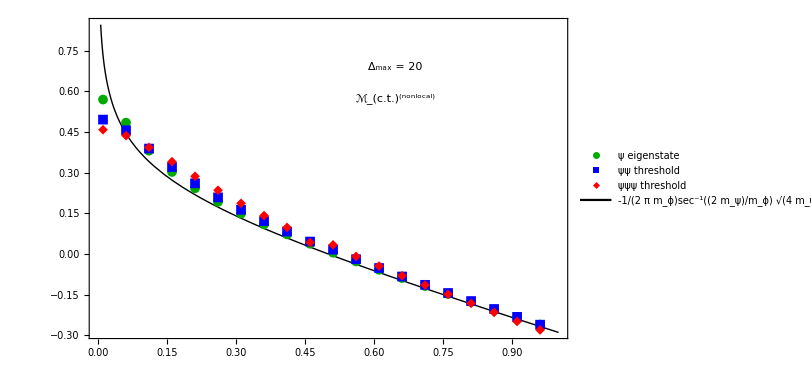

```mathematica
pltStateDependenceNonlocal=Block[{ms=1},Show[
Plot[
-1/(2π)(+(√(4 mf^2-ms^2))/ms ArcSec[(2mf)/ms]),
{mf,0,1},
PlotStyle->Directive[Black,Thick]
],
ListPlot[
datStateDependence,
PlotStyle->{
Directive[Darker[Green],Thick],
Directive[Blue,Thick],
Directive[Red,Thick]
},
PlotMarkers->{Automatic,10}
],
Frame->True,
ImageSize->600,
FrameStyle->Directive[Black],
(*FrameLabel->{"𝓂_ψ/𝓂_ϕ","δ𝓂_ψ^2/ℊ^2"},*)
LabelStyle->{FontFamily->"Times",16,Black},
Epilog->{
Inset[
Text[{Subscript[ℳ, "c.t."]^("(nonlocal)")(*," from Q_+^2"*)}//Row//TraditionalForm,
BaseStyle->{FontFamily->"Times",22,Black}],
Scaled[{.64,.75}]
],
Inset[
Text["Δ_max = 20",
BaseStyle->{FontFamily->"Times",22,Black}],
Scaled[{.64,.85}]
],
Inset[
PointLegend[{Darker[Green],Blue,Red},{"ψ eigenstate","ψψ threshold","ψψψ threshold"},LegendMarkers->{Automatic,10},
LabelStyle->{FontFamily->"Times",16,Black}],
Scaled[{.66,.55}]
],
Inset[
LineLegend[{Directive[Black,Thick]},
{{-1/(2 π Subscript[m, ϕ]),ArcSec[(2 Subscript[m, ψ])/Subscript[m, ϕ]] √(-Subscript[m, ϕ]^2+4 Subscript[m, ψ]^2)}//Row//TraditionalForm},
LabelStyle->{FontFamily->"Times",16,Black}],
Scaled[{.76,.38}]
]
}
] ]
```

Scan fermion mass mf. Compute the mass shift of 1 fermion state, 2 fermion threshold and 3 fermion threshold of the Hamiltonian with the local counter-term (10.10).

```mathematica
datStateDependenceLocal=Monitor[Block[{Δmax=20,ms=1,(*mf=0.4,*)g=10^-4,pos},
Table[
pos=particleSector[0,nF,Δmax];
{mf,1/(nF^2 g^2)(
Eigenvalues[(ms^2 Hms[Δmax]+mf^2 Hmf[Δmax]
+g^2/(2π)Log[1.8 Δmax]Hmf[Δmax])[[pos,pos]]
+g^2oneLoopShift[Δmax,mf,ms][[nF]]]-
Eigenvalues[(ms^2 Hms[Δmax]+mf^2 Hmf[Δmax])[[pos,pos]]]
)[[-1]]},
{nF,1,3},{mf,0.01,1,0.01}]
],{nF,mf}];
```

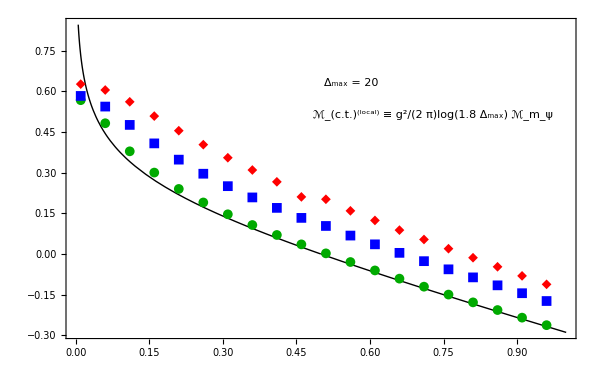

```mathematica
pltStateDependenceLocal=Block[{ms=1},Show[
Plot[
-1/(2π)(+(√(4 mf^2-ms^2))/ms ArcSec[(2mf)/ms]),
{mf,0,1},
PlotStyle->Directive[Black,Thick]
],
ListPlot[
datStateDependenceLocal[[;;,;;;;5]],
(*Joined->True,*)
PlotStyle->{
Directive[Darker[Green],Thick],
Directive[Blue,Thick],
Directive[Red,Thick]
},
PlotMarkers->{Automatic,10}
],
Frame->True,
ImageSize->600,
FrameStyle->Directive[Black],
(*FrameLabel->{"𝓂_ψ/𝓂_ϕ","δ𝓂_ψ^2/ℊ^2"},*)
LabelStyle->{FontFamily->"Times",16,Black},
Epilog->{
Inset[
Text[{Subscript[ℳ, "c.t."]^("(local)")," ≡ ",g^2/(2π),Log[1.8 Subscript[Δ, max]]," ",Subscript[ℳ, "m_ψ"]}//Row//TraditionalForm,
BaseStyle->{FontFamily->"Times",22,Black}],
Scaled[{.72,.7}]
],
Inset[
Text["Δ_max = 20",
BaseStyle->{FontFamily->"Times",22,Black}],
Scaled[{.56,.8}]
]
}
] ]
```

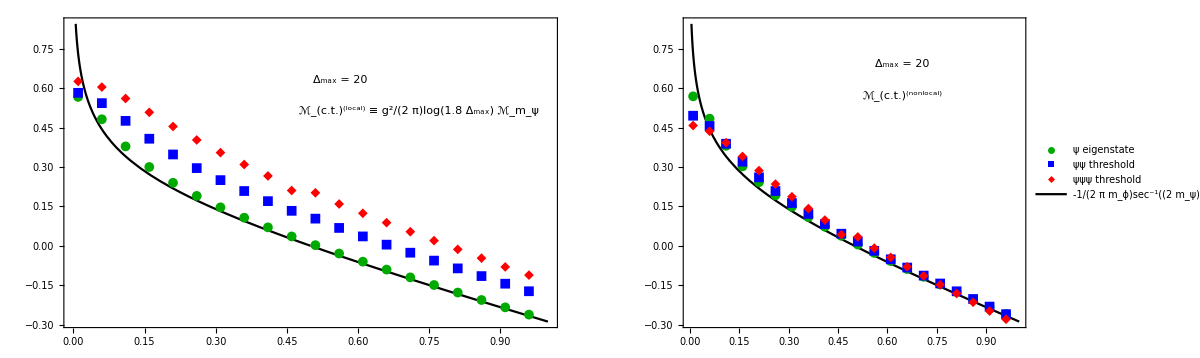
-Graphics-𝓂_ψ/𝓂_ϕδ𝓂_ψ^2/ℊ^2

```mathematica
pltStateDependenceGrid=Labeled[
GraphicsGrid[{
{pltStateDependenceLocal,pltStateDependenceNonlocal}
},
ImageSize->1200
],
{"𝓂_ψ/𝓂_ϕ",Rotate["δ𝓂_ψ^2/ℊ^2",90Degree]},{Bottom,Left},
LabelStyle->{FontFamily->"Times",22,Black}]
```

## Fig 21

We add to the previous two Hamiltonians by a local mass shift (eq 10.13)
-g^2/(2π)(Log[ms/mf])Hmf[Δmax]
besides the counter-term (10.10) or (10.11) that cancels the divergence, so that the fermion mass shift matches the covariant result. We will see the difference between using a non-local counter-term and using local counter-terms.

```mathematica
datStateDependenceCovariantNonlocal=Monitor[Block[{Δmax=20,ms=1,(*mf=0.4,*)g=10^-4,pos},
Table[
pos=particleSector[0,nF,Δmax];
{mf,1/(nF^2 g^2)(
Eigenvalues[(ms^2 Hms[Δmax]+(mf^2-g^2/(2π)Log[ms/mf]) Hmf[Δmax]
+(4g^2)(counter[Δmax]+counterScalar[Δmax]))[[pos,pos]]
+g^2oneLoopShift[Δmax,mf,ms][[nF]]
]-
Eigenvalues[(ms^2 Hms[Δmax]+mf^2 Hmf[Δmax])[[pos,pos]]]
)[[-1]]},
{nF,1,3},{mf,0.01,1,0.05}]
],{nF,mf}];
```

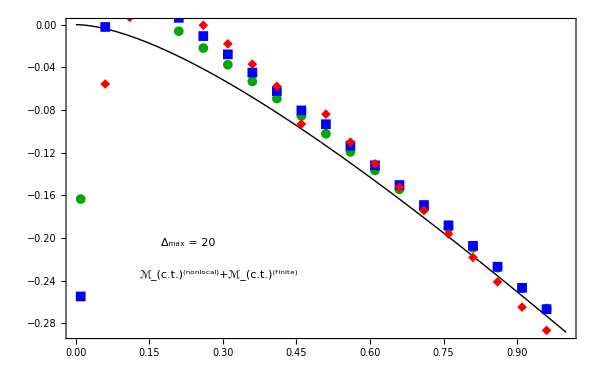

```mathematica
pltStateDependenceCovariantNonlocal=Block[{ms=1},Show[
Plot[
-1/(2π)(Log[ms/mf]+(√(4 mf^2-ms^2))/ms ArcSec[(2mf)/ms]),
{mf,0,1},
PlotStyle->Directive[Black,Thick]
],
ListPlot[
datStateDependenceCovariantNonlocal,
PlotStyle->{
Directive[Darker[Green],Thick],
Directive[Blue,Thick],
Directive[Red,Thick]
},
PlotMarkers->{Automatic,10}
],
Frame->True,
ImageSize->600,
FrameStyle->Directive[Black],
(*FrameLabel->{"𝓂_ψ/𝓂_ϕ","δ𝓂_ψ^2/ℊ^2"},*)
LabelStyle->{FontFamily->"Times",16,Black},
Epilog->{
Inset[
Text[{Subscript[ℳ, "c.t."]^("(nonlocal)"),"+",Subscript[ℳ, "c.t."]^("(finite)")(*," from Q_+^2"*)}//Row//TraditionalForm,
BaseStyle->{FontFamily->"Times",22,Black}],
Scaled[{.30,.2}]
],
Inset[
Text["Δ_max = 20",
BaseStyle->{FontFamily->"Times",22,Black}],
Scaled[{.24,.3}]
]
}
] ]
```

```mathematica
datStateDependenceCovariantLocal=Monitor[Block[{Δmax=20,ms=1,(*mf=0.4,*)g=10^-4,pos},
Table[
pos=particleSector[0,nF,Δmax];
{mf,1/(nF^2 g^2)(
Eigenvalues[(ms^2 Hms[Δmax]+(mf^2-g^2/(2π)Log[ms/mf]+g^2/(2π)Log[1.8 Δmax]) Hmf[Δmax])[[pos,pos]]
+g^2oneLoopShift[Δmax,mf,ms][[nF]]
]-
Eigenvalues[(ms^2 Hms[Δmax]+mf^2 Hmf[Δmax])[[pos,pos]]]
)[[-1]]},
{nF,1,3},{mf,0.01,1,0.05}]
],{nF,mf}];
```

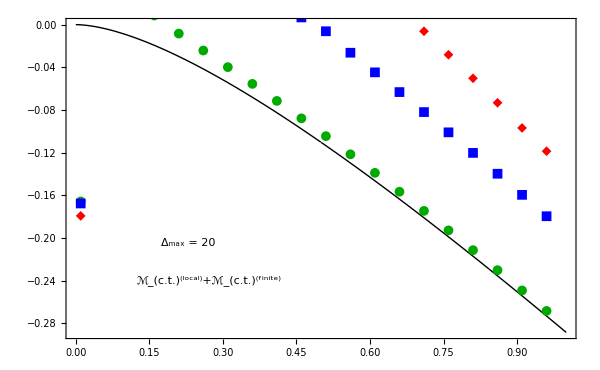

```mathematica
pltStateDependenceCovariantLocal=Block[{ms=1},Show[
Plot[
-1/(2π)(Log[ms/mf]+(√(4 mf^2-ms^2))/ms ArcSec[(2mf)/ms]),
{mf,0,1},
PlotStyle->Directive[Black,Thick]
],
ListPlot[
datStateDependenceCovariantLocal,
PlotStyle->{
Directive[Darker[Green],Thick],
Directive[Blue,Thick],
Directive[Red,Thick]
},
PlotMarkers->{Automatic,10}
],
Frame->True,
ImageSize->600,
FrameStyle->Directive[Black],
(*FrameLabel->{"𝓂_ψ/𝓂_ϕ","δ𝓂_ψ^2/ℊ^2"},*)
LabelStyle->{FontFamily->"Times",16,Black},
Epilog->{
Inset[
Text[{Subscript[ℳ, "c.t."]^("(local)"),"+",Subscript[ℳ, "c.t."]^("(finite)")(*," from local ",Subscript[ℳ, "ψ1/∂ψ"]*)}//Row//TraditionalForm,
BaseStyle->{FontFamily->"Times",22,Black}],
Scaled[{.28,.18}]
],
Inset[
Text["Δ_max = 20",
BaseStyle->{FontFamily->"Times",22,Black}],
Scaled[{.24,.3}]
]
}
] ]
```

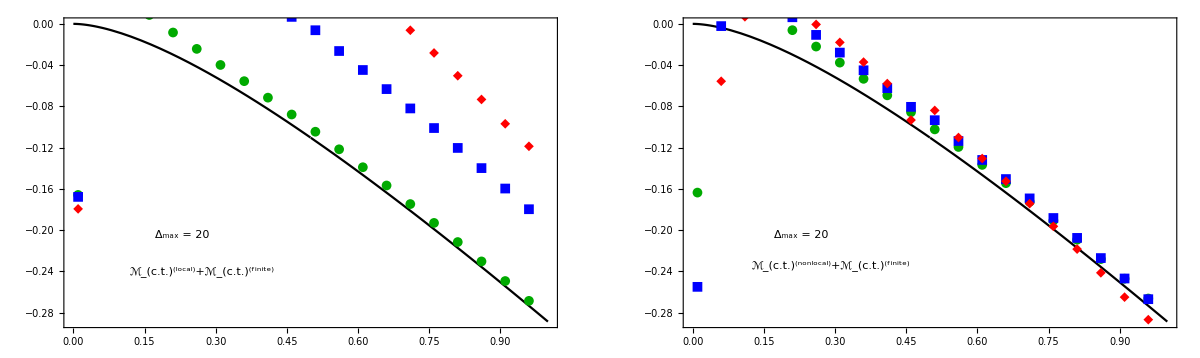
-Graphics-𝓂_ψ/𝓂_ϕδ𝓂_ψ^2/ℊ^2

```mathematica
pltStateDependenceCovariantGrid=Labeled[
GraphicsGrid[{
{pltStateDependenceCovariantLocal,pltStateDependenceCovariantNonlocal}
},
ImageSize->1200
],
{"𝓂_ψ/𝓂_ϕ",Rotate["δ𝓂_ψ^2/ℊ^2",90Degree]},{Bottom,Left},
LabelStyle->{FontFamily->"Times",22,Black}]
```

## The energy spectrum

## Fig 22

hamitonian[Δmax, mf, ms, g] is the Non-SUSY Yukawa Hamiltonian with non-local counter-term (10.11) and local counter-term (10.13). We scan the coupling g and diagonalize the Hamiltonian at each coupling.

### m_ψ=0.4 m_ϕ

```mathematica
spectrumD20Set1=Monitor[Block[
{Δmax=20},Table[
{g,#}&/@Sort[Eigenvalues[
hamitonian[Δmax,0.4,1,g],
-30
]],{g,0,1.0,0.005}]
]//Transpose,g];
```

Make a plot of the low mass eigenvalues as a function of g.

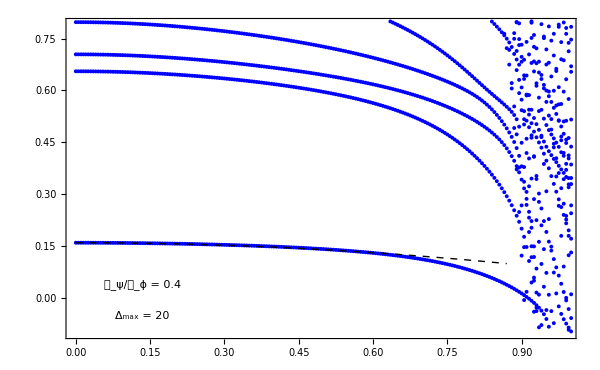

```mathematica
pltSpectrumD20Light=Show[ListPlot[
Select[
Flatten[spectrumD20Set1,1],
-0.1<=#[[2]]<=0.8&
],
PlotStyle->Blue,
PlotRange->{{0,0.99},{-0.099,0.79}},
Frame->True,
ImageSize->600,
FrameStyle->Directive[Black],
PlotMarkers->{Automatic,4},
(*FrameLabel->{"𝓂_ψ/𝓂_ϕ","μ_i^2/𝓂_ϕ^2"},*)
LabelStyle->{FontFamily->"Times",20,Black},
Epilog->{ 
Inset[
Text[Style["Δ_max = "<>ToString[20],{FontFamily->"Times",22,Black}]],
Scaled[{.15,.07}]
],
Inset[
Text[Style["𝓂_ψ/𝓂_ϕ = "<>ToString[0.4],{FontFamily->"Times",22,Black}]],
Scaled[{.15,.17}]
]
}
],
With[{ms=1,mf=0.4},Plot[
mf^2-g^2/(2π)(Log[ms/mf]+(√(4 mf^2-ms^2))/ms ArcSec[(2mf)/ms]),
{g,0,0.87},
PlotStyle->Directive[Black,Thick,Dashed]
]
]
]
```

### m_ψ=0.8 m_ϕ

```mathematica
spectrumD20Set2=Monitor[Block[
{Δmax=20},Table[
{g,#}&/@Sort[Eigenvalues[
hamitonian[Δmax,0.8,1,g],
-30
]],{g,0,1.0,0.01}]
]//Transpose,g];
spectrumD20Set3=Monitor[Block[
{Δmax=20},Table[
{g,#}&/@Sort[Eigenvalues[
hamitonian[Δmax,0.8,1,g],
-30
]],{g,1.01,2,0.01}]
]//Transpose,g];
```

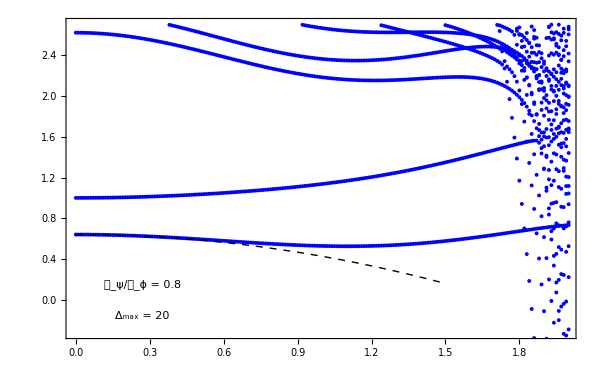

```mathematica
pltSpectrumD20Heavy=Show[ListPlot[
Select[
Join[
Flatten[spectrumD20Set2,1],
Flatten[spectrumD20Set3,1]
],
-1<=#[[2]]≤2.7&
],
PlotStyle->Blue,
PlotMarkers->{Automatic,4},
PlotRange->{{0,1.99},{-0.32,2.7}},
Frame->True,
ImageSize->600,
FrameStyle->Directive[Black],
(*FrameLabel->{"𝓂_ψ/𝓂_ϕ","μ_i^2/𝓂_ϕ^2"},*)
LabelStyle->{FontFamily->"Times",20,Black},
Epilog->{ 
Inset[
Text[Style["Δ_max = "<>ToString[20],{FontFamily->"Times",22,Black}]],
Scaled[{.15,.07}]
],,
Inset[
Text[Style["𝓂_ψ/𝓂_ϕ = "<>ToString[0.8],{FontFamily->"Times",22,Black}]],
Scaled[{.15,.17}]
]
}
],
With[{ms=1,mf=0.8},Plot[
mf^2-g^2/(2π)(Log[ms/mf]+(√(4 mf^2-ms^2))/ms ArcSec[(2mf)/ms]),
{g,0,1.5},
PlotStyle->Directive[Black,Thick,Dashed]
]
]
]
```

### Final plot

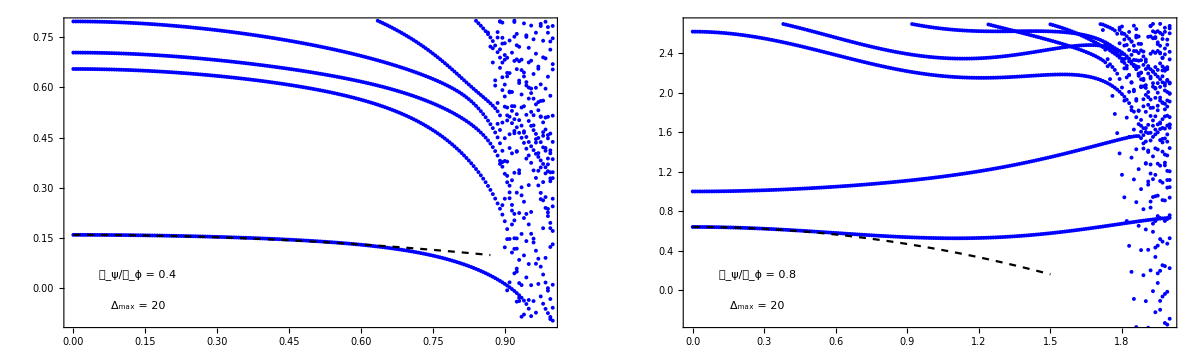
-Graphics-ℊ/𝓂_ϕμ_i/𝓂_ϕ

```mathematica
pltSpectrumGridTwo=Labeled[GraphicsGrid[{
{pltSpectrumD20Light,pltSpectrumD20Heavy}
},
ImageSize->1200],
{"ℊ/𝓂_ϕ",Rotate["μ_i/𝓂_ϕ",90Degree]},{Bottom,Left},
LabelStyle->{FontFamily->"Times",22,Black}]
```

## Spectral density

## define

```mathematica
(* position of 2 fermion 0 scalar states in the list of states truncated by Δmax *)
posψψ[Δmax_]:=Position[flattenedStates[[cut[Δmax]]],assoc_/;((#nF==2&&#nB==0)&[assoc]),1,Heads->False]//Flatten
```

```mathematica
(* For example, the position of ψψ states in the Δmax=5 basis is the following *)
posψψ[5]
```

{2,3}

```mathematica
(* Then we can extract these state by first restricting the basis to Δmax=5 and extract the correstponding positions *)
flattenedStates[[cut[5]]][[%]]//TableForm
```

<|nB→0,degB→0,nF→2,degF→1,l→0,states→{{{{1.}}}}|>
<|nB→0,degB→0,nF→2,degF→3,l→0,states→{{{{0.408248,-0.912871}}}}|>

```mathematica
(* position of 0 fermion 2 scalar states in the list of states truncated by Δmax *)
posϕϕ[Δmax_]:=Position[flattenedStates[[cut[Δmax]]],assoc_/;((#nF==0&&#nB==2)&[assoc]),1,Heads->False]//Flatten
posϕϕ[5]
flattenedStates[[cut[5]]][[%]]
```

{11,12}

{<|nB→2,degB→0,nF→0,degF→0,l→0,states→{{{{1.}}}}|>,<|nB→2,degB→2,nF→0,degF→0,l→0,states→{{{{0.632456},{-0.774597}}}}|>}

```mathematica
(* position of 0 fermion 1 scalar state in the list of states truncated by Δmax *)
posϕ[Δmax_]:=Position[flattenedStates[[cut[Δmax]]],assoc_/;((#nF==0&&#nB==1)&[assoc]),1,Heads->False]//Flatten//First
```

```mathematica
(* position of 0 fermion 3 scalar states in the list of states truncated by Δmax *)
posϕ3[Δmax_]:=Position[flattenedStates[[cut[Δmax]]],assoc_/;((#nF==0&&#nB==3)&[assoc]),1,Heads->False]//Flatten
posϕ3[5]
flattenedStates[[cut[5]]][[%]]
```

{18,19}

{<|nB→3,degB→0,nF→0,degF→0,l→0,states→{{{{1.}}}}|>,<|nB→3,degB→2,nF→0,degF→0,l→0,states→{{{{0.755929},{-0.654654}}}}|>}

```mathematica
(* The overlap ⟨ψ∂ψ(0)|[ψψ]_l, p⟩. Used in T_(--) spectral density. *)
ψdψList[Δmax_]:=Table[√((5+2 l)/(2π(1+l) (2+l) (3+l) (4+l)))//N,{l,1,Δmax-2,2}]
```

```mathematica
(* The overlap ⟨∂ϕ∂ϕ(0)|∂ϕ∂ϕ, p⟩. Used in T_(--) spectral density. *)
dϕdϕOvlap=1/(√(12 π));
```

```mathematica
(* Diagonalize the Hamiltonian Pp whose truncation is Δmax, and return the info of mass gap, eigenvalues, and eigenvectors' overlap with various special states. 
ops is optional, which is passed to the second argument of Eigensystem[Pp, ops] 
*)
spectralOptions[Δmax_,Pp_,ops___]:=Block[
{
evals,evecs,ψψovlaps,mGap,ϕϕovlaps(*,ρ0b,ρ0f*)
},
{evals,evecs}=SortBy[Eigensystem[Pp,ops
(*Method->{"FEAST","Interval"->interval(*{-1.0,-0.9}*)}*)
]//Transpose,Abs[First[#]]&]//Transpose;
evals=evals//Sqrt;
evecs=evecs;
mGap=evals[[1]];
ψψovlaps=evecs[[;;,posψψ[Δmax]]];
ϕϕovlaps=evecs[[;;,posϕϕ[Δmax]]];
<|
"Δmax"->Δmax,
"evals"->evals,
"mGap"->mGap,
"ψψovlaps"->ψψovlaps,
"ϕϕovlaps"->ϕϕovlaps,
"ψovlaps"->evecs[[;;,1]],
"ϕovlaps"->evecs[[;;,posϕ[Δmax]]],
"ϕ3ovlaps"->evecs[[;;,posϕ3[Δmax]]]
|>
]
```

```mathematica
(* Δmax=6 example *)
spectralOptions[6,hamitonian[6,1,1,0](* optional arguments of Eigenvalue[mat,ops] *)]
```

<|Δmax→6,evals→{1.,1.,2.05949,2.05949,2.26429,2.26429,2.66595,2.66595,3.24342,3.25576,3.58789,3.58789,3.6481,3.71753,4.18254,4.41711,4.58258,4.65158,4.77589,5.14269,5.15348,5.27107,5.3964,5.47089,5.53635,5.53635,5.76264,5.89495,5.9396,6.43296,6.50166,6.6495,6.7082,6.76759,7.01362,7.04499,7.2111,7.53183,8.12404,8.12404},mGap→1.,ψψovlaps→{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.870746,-0.491733},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.491733,0.870746},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}},ϕϕovlaps→{{0.,0.,0.},{0.,0.,0.},{0.813577,-0.544369,0.204341},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{-0.551866,-0.612235,0.566226},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.183131,0.573437,0.798519},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}},ψovlaps→{0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},ϕovlaps→{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},ϕ3ovlaps→{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.873185,-0.429754,-0.22991},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.487326,0.777353,0.397789},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.0077695,-0.459385,0.888204},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}|>

## Fig 23 - C function

Compute the Zamolodchikov C function at different Δ_max, different coupling and different m_ψ, and reproduce Figure 23.

### m_ψ=0.4 m_ϕ

```mathematica
dataCFuncD16Set1=Monitor[Block[
{mf=0.4,ms=1,Δmax=16,
dat,evals,ψψovlaps,ϕϕovlaps,intRho},
Table[
dat=spectralOptions[Δmax,
hamitonian[Δmax,mf,ms,g],
-100(* only need the smallest 100 eigenstates *)
];
evals=dat["evals"];  (* list of eigenvalues *)
ψψovlaps=dat["ψψovlaps"]; (* eigenstates' overlap with 2ψ states *)
ϕϕovlaps=dat["ϕϕovlaps"]; (* eigenstates' overlap with 2ϕ states *)
intRho=12 π Accumulate[(ψψovlaps.ψdψList[Δmax]+ϕϕovlaps⟦1;;All,1⟧ dϕdϕOvlap)^2];
(* Compute the integrated spectral density of T_(--) *)
g->Thread[{evals,intRho}],
{g,Range[0,0.8,0.1]
}
]//Association
],g];
```

```mathematica
dataCFuncD20Set1=Monitor[Block[
{mf=0.4,ms=1,Δmax=20,
dat,evals,ψψovlaps,ϕϕovlaps,intRho},
Table[
dat=spectralOptions[Δmax,
hamitonian[Δmax,mf,ms,g],
-200
];
evals=dat["evals"];
ψψovlaps=dat["ψψovlaps"];
ϕϕovlaps=dat["ϕϕovlaps"];
intRho=12 π Accumulate[(ψψovlaps.ψdψList[Δmax]+ϕϕovlaps⟦1;;All,1⟧ dϕdϕOvlap)^2];
g->Thread[{evals,intRho}],
{g,{0,0.8}}
]//Association
],g];
```

```mathematica
lgCFunc1=LineLegend[
{
Directive[Blue,Dashed],
Directive[Red,Dashed],
Directive[Blue],
Directive[Red]
},
Join[
("Δ_max = 16, ℊ/𝓂_ϕ = "<>ToString[#])&/@{0,0.8},
("Δ_max = 20, ℊ/𝓂_ϕ = "<>ToString[#])&/@{0,0.8}
],
LabelStyle->{FontFamily->"Times",16,Black},
LegendMarkers->{None,None,{"●",8},{"●",8}},
LegendFunction->(Framed[#1, FrameMargins -> 0] & )
]
```

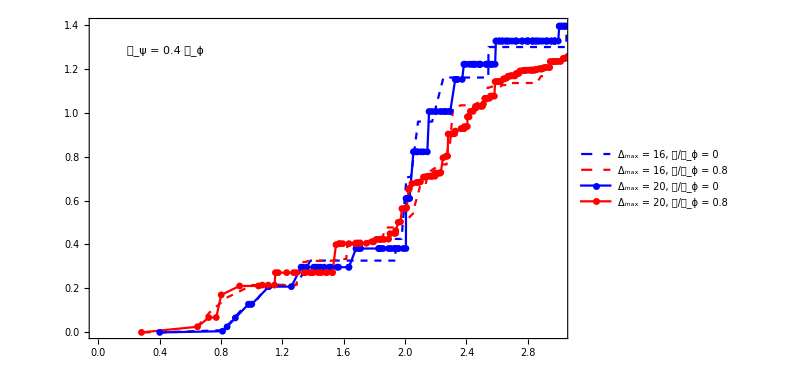

```mathematica
plotCFuncSet1=ListPlot[
{
dataCFuncD16Set1[[1]],
dataCFuncD16Set1[[-1]],
dataCFuncD20Set1[[1]],
dataCFuncD20Set1[[-1]]
},
Joined->True,
PlotRange->{{0,3},{0,1.4}},
PlotMarkers->{None,None,{"●",7},{"●",7}},
PlotStyle->{
Directive[Blue,Dashed],
Directive[Red,Dashed],
Directive[Blue],
Directive[Red]
},
Frame->True,
ImageSize->600,
FrameStyle->Directive[Black],
(*FrameLabel->{"𝓂_ψ/𝓂_ϕ","μ_i^2/𝓂_ϕ^2"},*)
LabelStyle->{FontFamily->"Times",20,Black},
Epilog->{ 
Inset[
Text[Style["𝓂_ψ = "<>ToString[.4]<>" 𝓂_ϕ",{FontFamily->"Times",20,Black}]],
Scaled[{.16,.9}]
],
Inset[
lgCFunc1,
Scaled[{.25,.65}]
]
}
]
```

### m_ψ=0.8 m_ϕ

```mathematica
dataCFuncD16Set2=Monitor[Block[
{mf=0.8,ms=1,Δmax=16,
dat,evals,ψψovlaps,ϕϕovlaps,intRho},
Table[
dat=spectralOptions[Δmax,
hamitonian[Δmax,mf,ms,g],
-200
];
evals=dat["evals"];
ψψovlaps=dat["ψψovlaps"];
ϕϕovlaps=dat["ϕϕovlaps"];
intRho=12 π Accumulate[(ψψovlaps.ψdψList[Δmax]+ϕϕovlaps⟦1;;All,1⟧ dϕdϕOvlap)^2];
g->Thread[{evals,intRho}],
{g,{0,1.8}}
]//Association
],g];
```

```mathematica
dataCFuncD20Set2=Monitor[Block[
{mf=0.8,ms=1,Δmax=20,
dat,evals,ψψovlaps,ϕϕovlaps,intRho},
Table[
dat=spectralOptions[Δmax,
hamitonian[Δmax,mf,ms,g],
-200
];
evals=dat["evals"];
ψψovlaps=dat["ψψovlaps"];
ϕϕovlaps=dat["ϕϕovlaps"];
intRho=12 π Accumulate[(ψψovlaps.ψdψList[Δmax]+ϕϕovlaps⟦1;;All,1⟧ dϕdϕOvlap)^2];
g->Thread[{evals,intRho}],
{g,{0,1.8}}
]//Association
],g];
```

```mathematica
lgCFunc2=LineLegend[
{
Directive[Blue,Dashed],
Directive[Red,Dashed],
Directive[Blue],
Directive[Red]
},
Join[
("Δ_max = 16, ℊ/𝓂_ϕ = "<>ToString[#])&/@{0,1.8},
("Δ_max = 20, ℊ/𝓂_ϕ = "<>ToString[#])&/@{0,1.8}
],
LabelStyle->{FontFamily->"Times",16,Black},
LegendMarkers->{None,None,{"●",8},{"●",8}},
LegendFunction->(Framed[#1, FrameMargins -> 0] & )
]
```

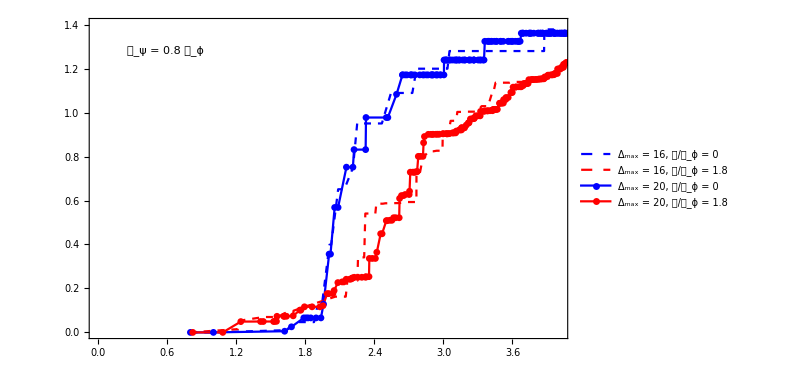

```mathematica
plotCFuncSet2=ListPlot[
{
dataCFuncD16Set2[[1]],
dataCFuncD16Set2[[-1]],
dataCFuncD20Set2[[1]],
dataCFuncD20Set2[[-1]]
},
Joined->True,
PlotRange->{{0,4},{0,1.4}},
PlotMarkers->{None,None,{"●",7},{"●",7}},
PlotStyle->{
Directive[Blue,Dashed],
Directive[Red,Dashed],
Directive[Blue],
Directive[Red]
},
Frame->True,
ImageSize->600,
FrameStyle->Directive[Black],
(*FrameLabel->{"𝓂_ψ/𝓂_ϕ","μ_i^2/𝓂_ϕ^2"},*)
LabelStyle->{FontFamily->"Times",20,Black},
Epilog->{ 
Inset[
Text[Style["𝓂_ψ = "<>ToString[.8]<>" 𝓂_ϕ",{FontFamily->"Times",20,Black}]],
Scaled[{.16,.9}]
],
Inset[
lgCFunc2,
Scaled[{.25,.65}]
]
}
]
```

### Final plot

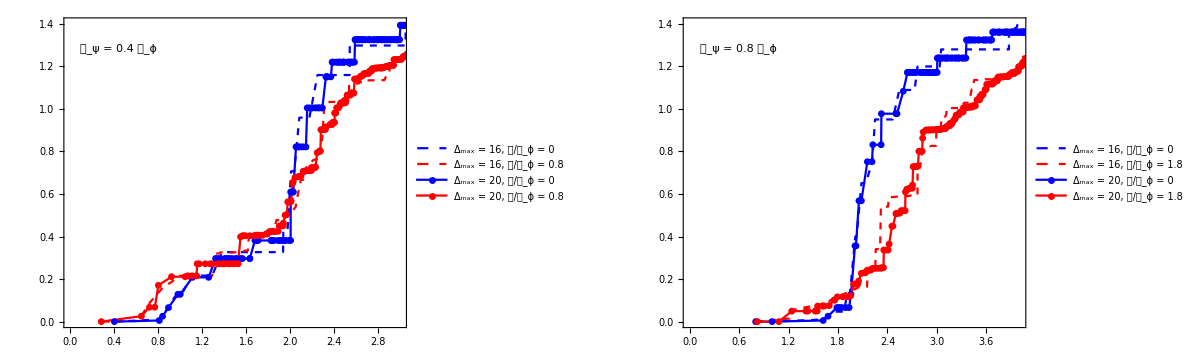
-Graphics-C(μ)μ/𝓂_ϕ

```mathematica
plotCFuncAll=Labeled[
GraphicsGrid[{
{plotCFuncSet1,plotCFuncSet2}
},
ImageSize->1200
],
{Rotate["C(μ)",90Degree],"μ/𝓂_ϕ"},{Left,Bottom},
LabelStyle->{FontFamily->"Times",24,Black}
]
```

## Fig 24 - ⟨ϕϕ⟩ correlator

### Compute the integrated spectral density of ϕ operator, and fit to the integrated Breit-Wigner function

```mathematica
dataPhiSpectralDensityD20Set1=Monitor[Block[
{mf=0.4,ms=1,Δmax=20,
dat,evals,ovlaps,dμ=0.01,nμ=200,
bins,μs,j
},
Table[
dat=spectralOptions[Δmax,
hamitonian[Δmax,mf,ms,g],
-100
];
Append[dat,"g"->g],
{g,{.3,.5,.7}}
]
],g];
```

```mathematica
lg1=LineLegend[
{Directive[Blue,Thick],Directive[Red,Dashed]},
{"ℊ/𝓂_ϕ = 0.3","ℊ/𝓂_ϕ = 0.7"},
(*LegendMarkers->{{"●",10},{"▲",10}},*)
LabelStyle->{FontFamily->"Times New Roman",16},
LegendMarkers->{Automatic,10}
]
```

{0.00300814 (165.947-105.645 ArcTan[105.645 (0.96302-s)]),0.00590857 (79.6031-50.6769 ArcTan[50.6769 (0.92361-s)])}

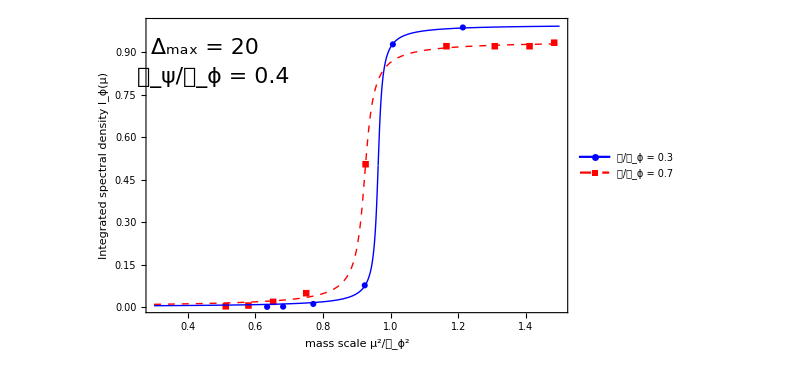

```mathematica
plotsBWFitD20Collection=Block[
{dat,fit,g,mGap,peak,dat2,model},
(* Fit the ⟨ϕ|μ⟩ integrated spectral density to this model.
The model is the integral of Breit-Wigner bump. *)
model=(-ArcTan[(M^2-s)/(M Γ)]/(M Γ)+π/(2M Γ))*(M Γ)/π*const;
dat2=Table[
dat=Select[
Thread[{#evals^2,Chop[#ϕovlaps]^2//Accumulate}]&@dataPhiSpectralDensityD20Set1[[i]],
0.3<#[[1]]<1.5&
];
g=#g&@dataPhiSpectralDensityD20Set1[[i]];
mGap=#mGap&@dataPhiSpectralDensityD20Set1[[i]];
fit=FindFit[
dat,model,{const,{M,1},{Γ,1}},s
];
{dat,g,mGap,fit,peak},
{i,{1,3}}];
Print[
model/.(*fit*)dat2[[;;,4]]//Evaluate
];
Show[
ListPlot[
dat2[[;;,1]],Axes->False,PlotStyle->{Blue,Red},PlotMarkers->Automatic
],
Plot[
model/.dat2[[;;,4]]//Evaluate,{s,0.3,1.5},
PlotStyle->{Directive[Blue,Thick],Directive[Red,Dashed,Thick]},
PlotPoints->100,MaxRecursion->10
],
PlotRange->{{0.3,1.5},{0,1.0}},
ImageSize->600,
Frame->True,
FrameStyle->Black,
FrameLabel->{"mass scale μ^2/𝓂_ϕ^2","Integrated spectral density I_ϕ(μ)"},
LabelStyle->{FontFamily->"Times New Roman",16},
Epilog->{
Inset[
Style["Δ_max = 20",{FontFamily->"Times New Roman",22}],
Scaled[{.14,.9}]
],
Inset[
Style["𝓂_ψ/𝓂_ϕ = 0.4",{FontFamily->"Times New Roman",22}],
Scaled[{.16,.8}]
],
Inset[
lg1,Scaled[{.16,.65}]
]
}
]
]
```

### Use the fitted Breit-Wigner function, plot the peak of ⟨ϕ|μ⟩ function

```mathematica
tabBWPeakD20=Table[Block[
{dat,fit,g,mGap,peak},
dat=Select[
Thread[{(#evals)^2,Chop[#ϕovlaps]^2//Accumulate}]&@dataPhiSpectralDensityD20Set1[[i]],
0.3<#[[1]]<1.5&
];
fit=FindFit[
dat,(-ArcTan[(M^2-s)/(M Γ)]/(M Γ)+π/(2M Γ))*(M Γ)/π*const,{const,{M,1},{Γ,1}},s
];
1/((s-M^2)^2+M^2 Γ^2)*(M Γ)/π*const/.fit
],{i,3}];
```

```mathematica
lg2=LineLegend[
{Directive[Blue,Thick],Directive[Red,Dashed]},
{"ℊ/𝓂_ϕ = 0.3","ℊ/𝓂_ϕ = 0.7"},
(*LegendMarkers->{{"●",10},{"▲",10}},*)
LabelStyle->{FontFamily->"Times New Roman",16}
]
```

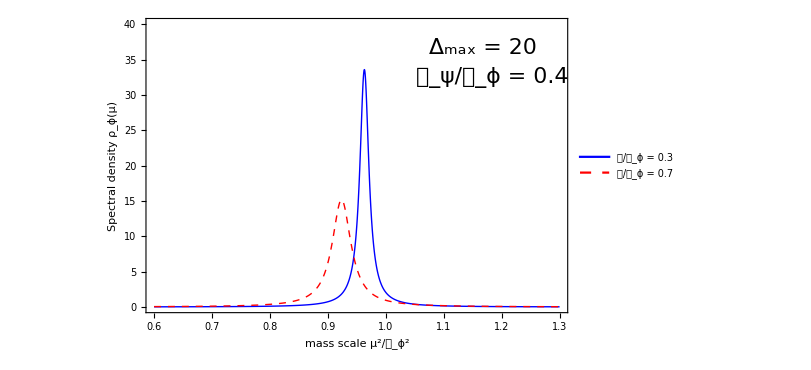

```mathematica
plotBWPeaksCollection=Show[
Plot[
tabBWPeakD20[[{1,-1}]]//Evaluate,
{s,.6,1.3},
PlotRange->{0,40},
PlotStyle->{Directive[Blue,Thick],Directive[Red,Dashed,Thick]}
],
ImageSize->600,
Frame->True,
FrameStyle->Black,
FrameLabel->{"mass scale μ^2/𝓂_ϕ^2","Spectral density ρ_ϕ(μ)"},
LabelStyle->{FontFamily->"Times New Roman",16},
Epilog->{
Inset[
Style["Δ_max = 20",{FontFamily->"Times New Roman",22}],
Scaled[{.8,.9}]
],
Inset[
Style["𝓂_ψ/𝓂_ϕ = 0.4",{FontFamily->"Times New Roman",22}],
Scaled[{.82,.8}]
],
Inset[
lg2,Scaled[{.82,.65}]
]
}
]
```